```mathematica
Clear[H,A,B,x1,x0,psi,out,Dmat,d1,d2,d3,d4,psi0,U,Re0,Re1,Im1,Im0]
Clear[sigX,sigZ,sigY,theta1,theta2,theta3,alpha]
(* Section used for universal objects (pauli's, H, etc.) and functions. If new functions need to be written/tested use a new cell beneath and then merge. 
*)

sigX = PauliMatrix[1];
sigY = PauliMatrix[2];
sigZ = PauliMatrix[3];
H = 1/(Sqrt[2])*{{1,1},{1,-1}};

rz[thetaZ_] := Cos[thetaZ/2]*IdentityMatrix[2] - I*Sin[thetaZ/2]*sigZ;
rx[thetaX_] :=Cos[thetaX/2]*IdentityMatrix[2] - I*Sin[thetaX/2]*sigX;

prod[psi_,phi_]:=( psi.Conjugate[phi])*(phi.Conjugate[psi]);

buildU[alpha_,theta1_,theta2_,theta3_]:= Exp[I*alpha]*rz[theta1].rx[theta2].rz[theta3];
getArgMins[psi_,phi_,params]:=Module[{Im0,Im1,Re0,Re1},
Re0 = (Re[phi[[1]]] - Re[psi[[1]]])^2;
Re1 = (Re[phi[[2]]] - Re[psi[[2]]])^2;
Im0 = (Im[phi[[1]]] - Im[psi[[1]]])^2;
Im1 = (Im[phi[[2]]] - Im[psi[[2]]])^2;
Return[NArgMin[Re0+Re1+Im0+Im1,params]];
]

testMatrixEquality[A_,B_]:=Module[{a,b,n,i,diff,eps},
a= Flatten[A];
b = Flatten[B];
If[Length[a]==Length[b],a = 1a;,Return[False]];
n = Length[a];
eps = 10^(-14);
For[i=1,i≤ Length[a],i++,
diff = Abs[a[[i]] - b[[i]]];
If[diff < eps,Continue,Return[False]];
];
Return[True];
]

getOptDmat[U_,n_] := Module[{A,B,psi,psi0,t,AtU,UtB,Dmat,d1,d2 ,d3,d4,finalMat,phi,temp,tot},
t = {0,0,0,0};
For[i=0,i<n,i++,
(*Print[StringForm["First For Loop: ``" ,i]];*)
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
psi0 = Normalize[RandomComplex[{-1-I,1+I},2]];
psi = B.H.A.psi0;
psi0 = {psi0[[1]],0,psi0[[2]],0};
AtU= ArrayFlatten[TensorProduct[A,U]];
UtB = ArrayFlatten[TensorProduct[ConjugateTranspose[U],B]];

Dmat = DiagonalMatrix[{d1,d2,d3,d4}];
finalMat = UtB.Dmat.AtU;

phi = finalMat.psi0;
phi = phi[[1;;2]]//Normalize//Simplify;
temp = getArgMins[psi,phi,{d1,d2,d3,d4}];
t = t +temp  ;
];

(* Line below converts a random t to unitary t. *)
t = t/Mean[Abs[t]];
Dmat = DiagonalMatrix[t];
Return[Dmat]
];

testOptMat[Dmat_,U_,n_]:=Module[{A,B,psi,psi0,AtU,UtB,finalMat,phi,results},
results = {};
For[i=0,i<n,i++,
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
psi0 = Normalize[RandomComplex[{-1-I,1+I},2]];
psi = B.H.A.psi0;
psi0 = {psi0[[1]],0,psi0[[2]],0};
AtU= ArrayFlatten[TensorProduct[A,U]];
UtB = ArrayFlatten[TensorProduct[ConjugateTranspose[U],B]];

finalMat = UtB.Dmat.AtU;

phi = finalMat.psi0;
phi = phi[[1;;2]]//Normalize//Simplify;
AppendTo[results,prod[phi,psi]];
];
Return[results]
]


getAverageOverlap[alpha_,theta1_,theta2_,theta3_,n_]:= Module[{U,Dmat,results},
U = buildU[alpha,theta1,theta2,theta3];

Dmat = getOptDmat[U,n];
results = testOptMat[Dmat,U,n];
Return[Mean[results]];
]


getAvgOverlapList[list_,n_]:=getAverageOverlap[list[[1]],list[[2]],list[[3]],list[[4]],n];
h[a_] := getAverageOverlap[Pi/2,a[[1]],a[[2]],Pi/2];

getStdOverlapList[list_,n_]:= Module[{U,Dmat,results},
U = buildU[list[[1]],list[[2]],list[[3]],list[[4]]];

Dmat = getOptDmat[U,n];
results = testOptMat[Dmat,U,n];
Return[StandardDeviation[results]];
]
```

```mathematica
getOptDMat3Q[U_,n_] := Module[{A,B,d1,d2,d3,d4,d5,d6,d7,d8,t,psi,phi,psi0,Dmat,temp,AtUtU,UtUtB,finalMat},
t = {0,0,0,0,0,0,0,0};
For[i=0,i<n,i++,
(*Print[StringForm["First For Loop: ``" ,i]];*)
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
psi0 = Normalize[RandomComplex[{-1-I,1+I},2]];
psi = B.H.A.psi0;
psi0 = TensorProduct[psi0,{1,0},{1,0}]//Flatten;
AtUtU= TensorProduct[ArrayFlatten[TensorProduct[A,U]],U]//ArrayFlatten;
UtUtB = TensorProduct[ArrayFlatten[TensorProduct[ConjugateTranspose[U],ConjugateTranspose[U]]],B]//ArrayFlatten;

Dmat = DiagonalMatrix[{d1,d2,d3,d4,d5,d6,d7,d8}];
finalMat = UtUtB.Dmat.AtUtU;

phi = finalMat.psi0;
phi = phi[[1;;2]]//Normalize//Simplify;
temp = getArgMins[psi,phi,{d1,d2,d3,d4,d5,d6,d7,d8}];
t = t +temp  ;
];
Return[DiagonalMatrix[t/n]];
]

getAvgOverlap3Q[alpha_,theta1_,theta2_,theta3_,n_] := Module[{U,Dmat,results},
U = buildU[alpha,theta1,theta2,theta3];
Dmat = getOptDMat3Q[U,n];
results = testOptMat3Q[Dmat,U,n];
Print[StringForm["Matrix: ``",MatrixForm[Dmat]]];
Return[Mean[results]]
]
```

```mathematica
Clear[alpha,theta1,theta2,theta3,AtU,UtB,Dmat,A,B,a1,a2,b1,b2,psi,psi0,psi1,Dmat,d1,d2,d3,d4,params]
(*
2 QUBIT ANALYTIC SECTION.

*)
testDmatUnitary[params_,angles_] := Module[{out},
out = (Exp[I*params]/. {theta1-> angles[[1]],theta2->angles[[2]]});
Return[If[N[Abs[out]]== Table[1,{i,1,Length[out]}],1,0]];
];

psi = {psi0,0,psi1,0};

U = buildU[ Pi/2,theta1,theta2, Pi/2]//Simplify;
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];

AtU= ArrayFlatten[TensorProduct[A,U]];
UtB =ArrayFlatten[TensorProduct[ConjugateTranspose[U],B]];

Dmat = DiagonalMatrix[Exp[I*{d1,d2,d3,d4}]];
finalMat = UtB.Dmat.AtU.psi//Simplify;

(*Print["phi"]*)
phi = FullSimplify[finalMat[[1;;2]],{Element[theta1,Reals],Element[theta2,Reals]}];
(*Print["psi"];*)
psi = B.H.A.{psi0,psi1}//Simplify;

eq1 = (phi[[1]] == 1/Sqrt[2]psi[[1]])/.{psi0->0,psi1-> 1}//Simplify;
eq2 = (phi[[1]] == 1/Sqrt[2]psi[[1]])/.{psi0->1,psi1->0}//Simplify;
eq3 = (phi[[2]] == 1/Sqrt[2]psi[[2]])/.{psi0->0,psi1-> 1}//Simplify;
eq4 = (phi[[2]] == 1/Sqrt[2]psi[[2]])/.{psi0->1,psi1->0}//Simplify;

params = {d1,d2,d3,d4};
params = (params/.Flatten[Normal/@Solve[{eq1,eq2,eq3,eq4},params]])//Simplify;
{d1,d2,d3,d4} = {d1,d2,d3,d4}/.{C[1]->0,C[2]->0,C[3]->0,C[4]->0};
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
Off[Power::infy]
Exp[I*params]//DiagonalMatrix//MatrixForm
grid =Flatten[ Table[{i,j},{i,0,2Pi,Pi/64},{j,0,2Pi,Pi/64}],1];
results = Map[testDmatUnitary[params,#]&,grid];
plotter = Table[Append[grid[[i]],results[[i]]],{i,1,Length[results]}];

Print["Since equations are solved analytically, this plot shows spots where the solved matrix is unitary. This is because all spots have a solvable matrix Dmat, their accuracy is 1.0."];
ListPlot3D[plotter,InterpolationOrder->1,AxesLabel->{"Theta 1","Theta 2","Test"}]
```

(ⅇ^((1.+0. ⅈ) (38.1267+Log[1/(3.61591×10^16+3.61591×10^16 Cos[theta2])])) | 0. | 0. | 0.
0. | (((-1.04083×10^-17-1. ⅈ) Cos[theta1]+(1.-1.04083×10^-17 ⅈ) Sin[theta1]) Sin[theta2])^(-1.+0. ⅈ) | 0. | 0.
0. | 0. | (-((0.+1.87212×10^16 ⅈ) Csc[theta2])/(1.87212×10^16 Cos[theta1]-(0.+1.87212×10^16 ⅈ) Sin[theta1]))^(1.+0. ⅈ) | 0.
0. | 0. | 0. | (1.83655×10^16+0. ⅈ) (-1/(1.83655×10^16-1.83655×10^16 Cos[theta2]))^(1.+0. ⅈ))

Since equations are solved analytically, this plot shows spots where the solved matrix is unitary. This is because all spots have a solvable matrix Dmat, their accuracy is 1.0.

-Graphics3D-

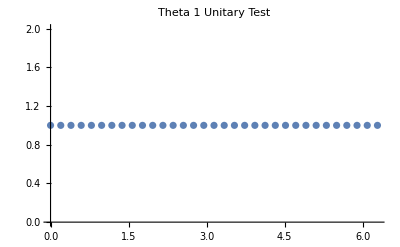

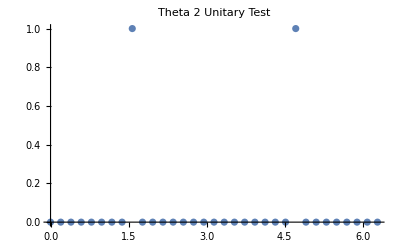

```mathematica
(* This section gives horizontal and Vertical Slices of the above graph. Probably useless. 
*)

table1 =Table[{i,testDmatUnitary[params,{i,Pi/2}]},{i,0,2Pi,Pi/16}];
ListPlot[table1,PlotLabel->"Theta 1 Unitary Test"]
table2 =Table[{i,testDmatUnitary[params,{Pi/2,i}]},{i,0,2Pi,Pi/16}];
ListPlot[table2,PlotLabel-> "Theta 2 Unitary Test" ]
```

```mathematica
(*
THIS IS 3 QUBIT VERSION OF ANALYTIC EQUATION SOLVING. First section contains general outline for solving for Dmat for a given U, second section preforms this same thing as a search over possible angles for U. This section still exists so that equations/outputs can be checked by hand as a function of theta1/theta2
*)


Clear[alpha,theta1,theta2,theta3,AtU,UtB,Dmat,A,B,a1,a2,b1,b2,psi,psi0,psi1,Dmat,d1,d2,d3,d4,d5,d6,d7,d8,params,AtUtU,UtUtB]
(* This function is to replace previous getArgMins that wouldn't quite work with this method, as it equated real/imaginary parts which doesn't quite work with psi0/psi1 method. *)

newGetArgMins[phi_,psi_,params_] :=Module[{eq1,eq2,eq3,eq4},
eq1 = Assuming[{Element[theta1,Reals],Element[theta2,Reals]},Abs[phi[[1]]- psi[[1]]]^2/.{psi0->0,psi1-> 1}]//Simplify;
eq2 =Assuming[{Element[theta1,Reals],Element[theta2,Reals]},Abs[phi[[1]] - psi[[1]]]^2/.{psi0->1,psi1->0}]//Simplify;
eq3 = Assuming[{Element[theta1,Reals],Element[theta2,Reals]},Abs[phi[[2]]- psi[[2]]]^2/.{psi0->0,psi1-> 1}]//Simplify;
eq4 = Assuming[{Element[theta1,Reals],Element[theta2,Reals]},Abs[phi[[2]] -psi[[2]]]^2/.{psi0->1,psi1->0}]//Simplify;
Return[NArgMin[eq1 + eq2 + eq3 + eq4 , params]];
];

(* This is supposed to test angles theta1, theta2 with two vectors for simulability, but I'm not too sure if it's even used.  *)
testAngles[thetaZ_,thetaX_,phi_,psi_]:=Module[{Dmat},
phi = (phi/.{theta1-> thetaZ,theta2-> thetaX})//Simplify;
Print[StringForm["Phi: ``",phi]];
Dmat = DiagonalMatrix[Exp[I*newGetArgMins[phi,psi,params]]];
Mean[Abs[testOptMat3Q[Dmat,U,10]]]//Return;
];

U = buildU[Pi/2,theta1,theta2,Pi/2];

(*A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];*)
A = IdentityMatrix[2];
B = IdentityMatrix[2];

AtU= ArrayFlatten[TensorProduct[A,U]];
UtB =ArrayFlatten[TensorProduct[ConjugateTranspose[U],B]];


AtUtU = ArrayFlatten[TensorProduct[AtU,U]];
UtUtB = ArrayFlatten[TensorProduct[ConjugateTranspose[U],UtB]];


params = {d1,d2,d3,d4,d5,d6,d7,d8};
Dmat = DiagonalMatrix[Exp[I*params]];

psi = Flatten[TensorProduct[{psi0,psi1},{1,0},{1,0}]];
finalMat = FullSimplify[ UtUtB.Dmat.AtUtU,{Element[theta1,Reals],Element[theta2,Reals]}];
phi = finalMat.psi;
(*Postselection*)
(*Print["Phi"]*)
phi = phi[[1;;2]]//Normalize//Simplify;
(*Print["psi"]*)
psi = B.H.A.{psi0,psi1};
```

```mathematica
Clear[Dmat]
params = {d1,d2,d3,d4,d5,d6,d7,d8};
```

```mathematica
(* This is the big function, given two angles it optimizes over parameters for Dmat and then gives the accuracy of the found matrix. Need to modularize this to make easier for 4/5 qubit gadgets and verification. 
*)
f[theta1_,theta2_]:= Module[{U,AtU,UtB,AtUtU,UtUtB,params,Dmat,d1,d2,d3,d4,d5,d6,d7,d8,d9,d10,d11,d12,d13,d14,d15,d16,psi,finalMat,phi,psi0,psi1,eq1,eq2,eq3,eq4},
U = buildU[Pi/2,theta1,theta2,Pi/2];
AtU= ArrayFlatten[TensorProduct[IdentityMatrix[2],U]];
UtB =ArrayFlatten[TensorProduct[ConjugateTranspose[U],IdentityMatrix[2]]];
AtUtU = ArrayFlatten[TensorProduct[AtU,U]];
UtUtB = ArrayFlatten[TensorProduct[ConjugateTranspose[U],UtB]];
(*AtUtU = ArrayFlatten[TensorProduct[AtUtU,U]];
UtUtB = ArrayFlatten[TensorProduct[ConjugateTranspose[U],UtUtB]];*)

params = {d1,d2,d3,d4,d5,d6,d7,d8};
(*params = {d1,d2,d3,d4,d5,d6,d7,d8,d9,d10,d11,d12,d13,d14,d15,d16};*)
Dmat = DiagonalMatrix[Exp[I*params]];

psi = Flatten[TensorProduct[{psi0,psi1},{1,0},{1,0}]];
finalMat = FullSimplify[ UtUtB.Dmat.AtUtU,{Element[theta1,Reals],Element[theta2,Reals]}];
phi = finalMat.psi;
(*Postselection*)
phi = phi[[5;;6]]//Normalize//Simplify;
psi = H.{psi0,psi1};

eq1 = Assuming[{Element[theta1,Reals],Element[theta2,Reals]},Abs[phi[[1]]- psi[[1]]]^2/.{psi0->0,psi1-> 1}]//Simplify;
eq2 =Assuming[{Element[theta1,Reals],Element[theta2,Reals]},Abs[phi[[1]] - psi[[1]]]^2/.{psi0->1,psi1->0}]//Simplify;
eq3 = Assuming[{Element[theta1,Reals],Element[theta2,Reals]},Abs[phi[[2]]- psi[[2]]]^2/.{psi0->0,psi1-> 1}]//Simplify;
eq4 = Assuming[{Element[theta1,Reals],Element[theta2,Reals]},Abs[phi[[2]] -psi[[2]]]^2/.{psi0->1,psi1->0}]//Simplify;
(* NArgMin gets the numerical min of sum of eq's over the params. Since the params are the angles of the complex numbers (and NArgMin only searches over reals) Dmat is guaranteed to be unitary, up to underflow errors.  *)
Dmat = DiagonalMatrix[Exp[I*NArgMin[eq1+eq2+eq3+eq4,params]]];

(*Print[StringForm["Determinant of Dmat: ``",Abs[Det[Dmat]]]];
Print[StringForm["Is Dmat Unitary: ``",testMatrixEquality[IdentityMatrix[16],ConjugateTranspose[Dmat].Dmat]]];*)

(* Note that each matrix is called with n = 100 samples to test test random inputs and A/B matrices. *)
{Mean[Abs[testOptMat3Q[Dmat,U,100]]],StandardDeviation[Abs[testOptMat3Q[Dmat,U,100]]]} // Return;
]

(* The test function used in f, but put here so can be changed easily (when postselecting over different outputs). *)
testOptMat3Q[Dmat_,U_,n_]:=Module[{A,B,AtU,UtB,AtUtU,UtUtB,psi,psi0,phi,results,finalMat},
results = {};
For[i=0,i<n,i++,
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
psi0 = Normalize[RandomComplex[{-1-I,1+I},2]];
psi = B.H.A.psi0;
psi0 = TensorProduct[psi0,{1,0},{1,0}]//Flatten;
AtU= ArrayFlatten[TensorProduct[A,U]];
UtB = ArrayFlatten[TensorProduct[ConjugateTranspose[U],B]];
AtUtU = ArrayFlatten[TensorProduct[AtU,U]];
UtUtB = ArrayFlatten[TensorProduct[ConjugateTranspose[U],UtB]];
(*AtUtU = ArrayFlatten[TensorProduct[AtUtU,U]];
UtUtB = ArrayFlatten[TensorProduct[ConjugateTranspose[U],UtUtB]];*)

finalMat = UtUtB.Dmat.AtUtU;

phi = finalMat.psi0;
phi = phi[[5;;6]]//Normalize//Simplify;
AppendTo[results,prod[phi,psi]];
];
Return[results]
]
(* Simple wrapper function so f can be called with a list generated by a table, as I don't know how to do this easier. 
*)
g[list_]:=f[list[[1]],list[[2]]];
```

{1.32536,1.37445,1.42353,1.47262,1.52171,1.5708,1.61988,1.66897,1.71806,1.76715,1.81623,1.86532,1.91441,1.9635,2.01258,2.06167,2.11076,2.15984,2.20893,2.25802,2.30711,2.35619,2.40528,2.45437,2.50346,2.55254,2.60163,2.65072,2.69981,2.74889,2.79798,2.84707,2.89616,2.94524,2.99433,3.04342,3.09251,3.14159,3.19068,3.23977,3.28885,3.33794,3.38703,3.43612,3.4852,3.53429,3.58338,3.63247,3.68155,3.73064,3.77973,3.82882,3.8779,3.92699,3.97608,4.02517,4.07425,4.12334,4.17243,4.22152,4.2706,4.31969,4.36878,4.41786,4.46695,4.51604}

{{1.32536,0.96231},{1.37445,0.978715},{1.42353,0.977453},{1.47262,0.996858},{1.52171,0.994491},{1.5708,0.999903},{1.61988,0.993546},{1.66897,0.997539},{1.71806,0.977186},{1.76715,0.951391},{1.81623,0.990248},{1.86532,0.989935},{1.91441,0.867737},{1.9635,0.962014},{2.01258,0.971624},{2.06167,0.939954},{2.11076,0.948264},{2.15984,0.926534},{2.20893,0.913471},{2.25802,0.903212},{2.30711,0.859046},{2.35619,0.835507},{2.40528,0.797896},{2.45437,0.772739},{2.50346,0.705226},{2.55254,0.69571},{2.60163,0.609882},{2.65072,0.628054},{2.69981,0.606897},{2.74889,0.586964},{2.79798,0.518635},{2.84707,0.546392},{2.89616,0.533513},{2.94524,0.534256},{2.99433,0.458444},{3.04342,0.459808},{3.09251,0.511358},{3.14159,0.528244},{3.19068,0.483557},{3.23977,0.492849},{3.28885,0.488025},{3.33794,0.517463},{3.38703,0.529478},{3.43612,0.503926},{3.4852,0.578137},{3.53429,0.58578},{3.58338,0.607665},{3.63247,0.659118},{3.68155,0.667395},{3.73064,0.674908},{3.77973,0.730315},{3.82882,0.777406},{3.8779,0.801374},{3.92699,0.823493},{3.97608,0.863506},{4.02517,0.90009},{4.07425,0.911485},{4.12334,0.932099},{4.17243,0.949006},{4.22152,0.937074},{4.2706,0.976024},{4.31969,0.980078},{4.36878,0.976386},{4.41786,0.984762},{4.46695,0.897893},{4.51604,0.995907}}

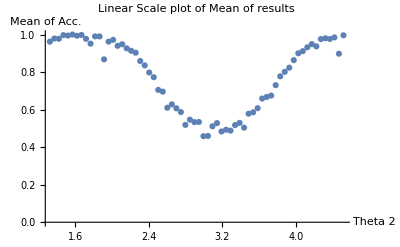

{{1.32536,0.0123842},{1.37445,0.0078684},{1.42353,0.00809031},{1.47262,0.00117782},{1.52171,0.00202317},{1.5708,0.0000334285},{1.61988,0.00228877},{1.66897,0.000801043},{1.71806,0.00684377},{1.76715,0.0180822},{1.81623,0.00392614},{1.86532,0.00374534},{1.91441,0.0529155},{1.9635,0.0149799},{2.01258,0.0110358},{2.06167,0.020496},{2.11076,0.020681},{2.15984,0.0239863},{2.20893,0.0334789},{2.25802,0.0437911},{2.30711,0.0670783},{2.35619,0.0922975},{2.40528,0.125379},{2.45437,0.153991},{2.50346,0.170663},{2.55254,0.191619},{2.60163,0.213599},{2.65072,0.262196},{2.69981,0.259792},{2.74889,0.276486},{2.79798,0.309183},{2.84707,0.307749},{2.89616,0.303942},{2.94524,0.328515},{2.99433,0.294894},{3.04342,0.317379},{3.09251,0.309577},{3.14159,0.309596},{3.19068,0.305297},{3.23977,0.316374},{3.28885,0.285251},{3.33794,0.284624},{3.38703,0.29526},{3.43612,0.306867},{3.4852,0.296488},{3.53429,0.279408},{3.58338,0.273367},{3.63247,0.25611},{3.68155,0.211465},{3.73064,0.189883},{3.77973,0.16122},{3.82882,0.138308},{3.8779,0.113384},{3.92699,0.0849274},{3.97608,0.0670076},{4.02517,0.0496155},{4.07425,0.0336045},{4.12334,0.0255874},{4.17243,0.0171192},{4.22152,0.0202976},{4.2706,0.0076195},{4.31969,0.00760799},{4.36878,0.00882071},{4.41786,0.00572643},{4.46695,0.0372488},{4.51604,0.00163466}}

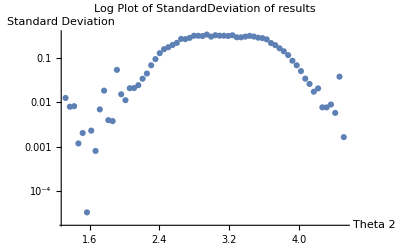

```mathematica
(* Test section, where f is used over a scan of a region and results are plotted. Note it is always centered about Pi/2, which is where U = H. 
*)
Clear[i,j,plotter, results, tab]

dx = N[Pi/(2^6)];
a = Pi/2 - 5*dx;
b = Pi/2 + 60*dx;

tab = Table[i,{i,a,b,dx}]
results = Table[f[Pi/2,tab[[i]]], {i,1,Length[tab]}];
plotter = Table[{tab[[i]],results[[i]][[1]]},{i,1,Length[tab]}]
ListPlot[plotter, PlotLabel->"Linear Scale plot of Mean of results",AxesLabel->{"Theta 2", "Mean of Acc."}]
plotter = Table[{tab[[i]],results[[i]][[2]]},{i,1,Length[tab]}]
ListLogPlot[plotter,PlotLabel->"Log Plot of StandardDeviation of results",AxesLabel->{"Theta 2","Standard Deviation"}]
```

```mathematica
Clear[a,b]
Flatten[TensorProduct[{0,1},{1,0},{0,1},{a,b}]]
```

{0,0,0,0,0,0,0,0,0,0,a,b,0,0,0,0}